```mathematica
data=Import[NotebookDirectory[]<>"lichtgeschwindigkeit.xlsx"][[1]]
```

{{Lightquelle,23.,1.},{Linse,33.,1.},{26 ns,8.4,2.},{30 ns,15.9,2.},{30 ns,25.,2.},{56 ns,3.5,3.},{56 ns,14.,3.},{58 ns,26.,3.},{84 ns,3.,4.},{86 ns,15.,4.},{86 ns,25.,4.}}

```mathematica
x1=3880;
x2=7890;
x3=11682;
```

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
distances=AssociationThread[Range[4],{0,x1,x2,x3}]
```

<|1→0,2→3880,3→7890,4→11682|>

```mathematica
processed={10 #[[2]]+distances[Round@#[[3]]]-230,StringSplit[#[[1]], " "][[1]]}&/@data
```

{{0.,Lightquelle},{100.,Linse},{3734.,26},{3809.,30},{3900.,30},{7695.,56},{7800.,56},{7920.,58},{11482.,84},{11602.,86},{11702.,86}}

```mathematica
dataCut={#[[1]],ToExpression[#[[2]]]}&/@processed[[3;;-1]]
```

{{3734.,26},{3809.,30},{3900.,30},{7695.,56},{7800.,56},{7920.,58},{11482.,84},{11602.,86},{11702.,86}}

```mathematica
Length[dataCut]
```

9

```mathematica
gaussReg[xdata_,ydata_,dydata_]:=With[{Δ=Total[1/#^2&/@ dydata]Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[xdata]}])^2},{1/Δ(Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}] Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), 1/Δ(Total[1/#^2&/@ dydata]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), Sqrt[1/Δ Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]], Sqrt[1/Δ Total[1/#^2&/@ dydata]]} ]
```

```mathematica
pars=gaussReg[dataCut[[All,1]],dataCut[[All,2]],ConstantArray[Sqrt[2] 4,9]]
```

{0.524984,0.00728383,4.96342,0.000593327}

```mathematica
N@Sqrt[2] 4
```

5.65685

```mathematica
2pars[[4]]/pars[[2]]^2*10^6
```

2.23668×10^7

```mathematica
2/pars[[2]]*10^(9)*10^(-3)
```

2.74581×10^8

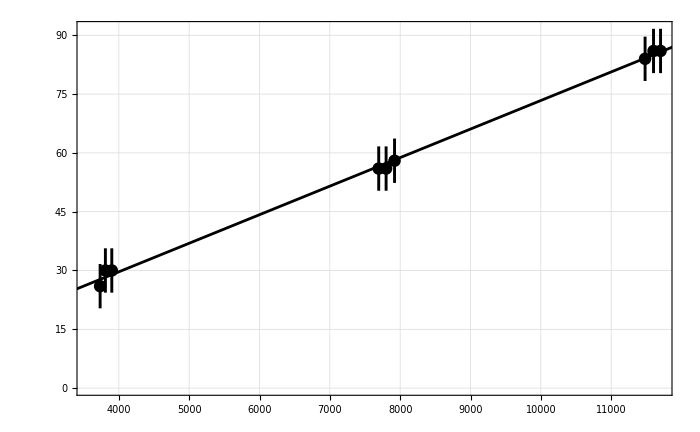

```mathematica
Show[ListPlot[{#[[1]],Around[#[[2]],Sqrt[2] 4]}&/@dataCut,PlotStyle->Directive[Black,Thickness[0.003]]],Plot[pars[[1]]+pars[[2]]x,{x,0,100000},PlotStyle->Black],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"lichtgeschwindigkeit.pdf",Show[ListPlot[{#[[1]],Around[#[[2]],Sqrt[2] 4]}&/@dataCut,PlotStyle->Directive[Black,Thickness[0.003]]],Plot[pars[[1]]+pars[[2]]x,{x,0,100000},PlotStyle->Black],pltsettings],Background->None];
```